```mathematica
$ImportFormats;
scatterdata=Import["C:\\Users\\shahn\\OneDrive\\Desktop\\data sheet.csv"];
```

```mathematica
(*making list of sigma values for each Q^2*)
sigma1= scatterdata[[2;;4,22]];
sigma2= scatterdata[[5;;8,22]];
sigma3= scatterdata[[9;;13,22]];
sigma4= scatterdata[[14;;17,22]];
sigma5= scatterdata[[18;;24,22]];
sigma6= scatterdata[[25;;28,22]];
sigma7= scatterdata[[29;;33,22]];
sigma8= scatterdata[[34;;39,22]];
sigma9= scatterdata[[40;;44,22]];
sigma10= scatterdata[[45;;46,22]];
sigma11= scatterdata[[47;;48,22]];
```

```mathematica
(*making list of epsilon values for each Q^2*)
eps1=scatterdata[[2;;4,3]];
eps2= scatterdata[[5;;8,3]];
eps3= scatterdata[[9;;13,3]];
eps4= scatterdata[[14;;17,3]];
eps5= scatterdata[[18;;24,3]];
eps6= scatterdata[[25;;28,3]];
eps7= scatterdata[[29;;33,3]];
eps8= scatterdata[[34;;39,3]];
eps9= scatterdata[[40;;44,3]];
eps10= scatterdata[[45;;46,3]];
eps11= scatterdata[[47;;48,3]];
```

```mathematica
(*making list of statistical error values for each Q^2*)
stat1 = scatterdata[[2;;4,12]];
stat2= scatterdata[[5;;8,12]];
stat3= scatterdata[[9;;13,12]];
stat4= scatterdata[[14;;17,12]];
stat5= scatterdata[[18;;24,12]];
stat6= scatterdata[[25;;28,12]];
stat7= scatterdata[[29;;33,12]];
stat8= scatterdata[[34;;39,12]];
stat9= scatterdata[[40;;44,12]];
stat10= scatterdata[[45;;46,12]];
stat11= scatterdata[[47;;48,12]];
```

```mathematica
(*making list of systamatic error values for each Q^2*)
syst1 = scatterdata[[2;;4,13]];
syst2= scatterdata[[5;;8,13]];
syst3= scatterdata[[9;;13,13]];
syst4= scatterdata[[14;;17,13]];
syst5= scatterdata[[18;;24,13]];
syst6= scatterdata[[25;;28,13]];
syst7= scatterdata[[29;;33,13]];
syst8= scatterdata[[34;;39,13]];
syst9= scatterdata[[40;;44,13]];
syst10= scatterdata[[45;;46,13]];
syst11= scatterdata[[47;;48,13]];
```

```mathematica
(*writing the sigma value with its corresponding error for each Q^2. The quadrature sum of systamatic and statistical errors are taken here*)
sigmaerror1 = Table[Around[sigma1[[i]],Sqrt[(stat1[[i]]*sigma1[[i]]/100)^2+(syst1[[i]]*sigma1[[i]]/100)^2]],{i,1,Length[sigma1]}];
sigmaerror2= Table[Around[sigma2[[i]], Sqrt[(stat2[[i]]*sigma2[[i]]/100)^2+(syst2[[i]]*sigma2[[i]]/100)^2]],{i,1,Length[sigma2]}];
sigmaerror3 = Table[Around[sigma3[[i]],Sqrt[(stat3[[i]]*sigma3[[i]]/100)^2+(syst3[[i]]*sigma3[[i]]/100)^2]],{i,1,Length[sigma3]}];
sigmaerror4 = Table[Around[sigma4[[i]], Sqrt[(stat4[[i]]*sigma4[[i]]/100)^2+(syst4[[i]]*sigma4[[i]]/100)^2]],{i,1,Length[sigma4]}];
sigmaerror5 = Table[Around[sigma5[[i]], Sqrt[(stat5[[i]]*sigma5[[i]]/100)^2+(syst5[[i]]*sigma5[[i]]/100)^2]],{i,1,Length[sigma5]}];
sigmaerror6 = Table[Around[sigma6[[i]], Sqrt[(stat6[[i]]*sigma6[[i]]/100)^2+(syst6[[i]]*sigma6[[i]]/100)^2]],{i,1,Length[sigma6]}];
sigmaerror7 = Table[Around[sigma7[[i]], Sqrt[(stat7[[i]]*sigma7[[i]]/100)^2+(syst7[[i]]*sigma7[[i]]/100)^2]],{i,1,Length[sigma7]}];
sigmaerror8 = Table[Around[sigma8[[i]], Sqrt[(stat8[[i]]*sigma8[[i]]/100)^2+(syst8[[i]]*sigma8[[i]]/100)^2]],{i,1,Length[sigma8]}];
sigmaerror9 = Table[Around[sigma9[[i]], Sqrt[(stat9[[i]]*sigma9[[i]]/100)^2+(syst9[[i]]*sigma9[[i]]/100)^2]],{i,1,Length[sigma9]}];
sigmaerror10 = Table[Around[sigma10[[i]],Sqrt[(stat10[[i]]*sigma10[[i]]/100)^2+(syst10[[i]]*sigma10[[i]]/100)^2]],{i,1,Length[sigma10]}];
sigmaerror11= Table[Around[sigma11[[i]], Sqrt[(stat11[[i]]*sigma11[[i]]/100)^2+(syst11[[i]]*sigma11[[i]]/100)^2]],{i,1,Length[sigma11]}];
```

```mathematica
(*Values of Subscript[τG, D]^2 for corresponding Q^2*)
Gd1 = scatterdata[[2;;4,26]];
Gd2= scatterdata[[5;;8,26]];
Gd3= scatterdata[[9;;13,26]];
Gd4= scatterdata[[14;;17,26]];
Gd5= scatterdata[[18;;24,26]];
Gd6= scatterdata[[25;;28,26]];
Gd7= scatterdata[[29;;33,26]];
Gd8= scatterdata[[34;;39,26]];
Gd9= scatterdata[[40;;44,26]];
Gd10= scatterdata[[45;;46,26]];
Gd11= scatterdata[[47;;48,26]];
```

```mathematica
(*Calculaton for Subscript[σ, r]/Subscript[τG, D]^2 for corresponding Q^2*)
sigmaGd1= sigmaerror1/Gd1;
sigmaGd2= sigmaerror2/Gd2;
sigmaGd3= sigmaerror3/Gd3;
sigmaGd4= sigmaerror4/Gd4;
sigmaGd5= sigmaerror5/Gd5;
sigmaGd6= sigmaerror6/Gd6;
sigmaGd7= sigmaerror7/Gd7;
sigmaGd8= sigmaerror8/Gd8;
sigmaGd9= sigmaerror9/Gd9;
sigmaGd10= sigmaerror10/Gd10;
sigmaGd11= sigmaerror11/Gd11;
```

```mathematica
(*Calculation for ftting function for the graph*)
fit1= Fit[Transpose[{eps1,sigma1/Gd1}], {1,x},x];
fit2= Fit[Transpose[{eps2,sigma2/Gd2}], {1,x},x];
fit3= Fit[Transpose[{eps3,sigma3/Gd3}], {1,x},x];
fit4= Fit[Transpose[{eps4,sigma4/Gd4}], {1,x},x];
fit5= Fit[Transpose[{eps5,sigma5/Gd5}], {1,x},x];
fit6= Fit[Transpose[{eps6,sigma6/Gd6}], {1,x},x];
fit7= Fit[Transpose[{eps7,sigma7/Gd7}], {1,x},x];
fit8= Fit[Transpose[{eps8,sigma8/Gd8}], {1,x},x];
fit9= Fit[Transpose[{eps9,sigma9/Gd9}], {1,x},x];
fit10= Fit[Transpose[{eps10,sigma10/Gd10}], {1,x},x];
fit11= Fit[Transpose[{eps11,sigma11/Gd11}], {1,x},x];
```

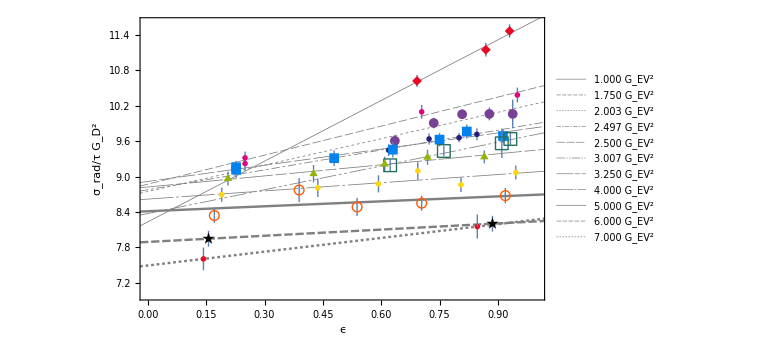

```mathematica
(*Graph of Subscript[σ, r]/Subscript[τG, D]^2*)
Show[Plot[{{fit1},{fit2},{fit3},{fit4},{fit5},{fit6},{fit7},{fit8},{fit9},{fit10},{fit11}},{x,-0.02,1.02},PlotStyle->{{Gray,Thickness[.001]},{Gray,Thickness[.001]},{Gray,Thickness[.001]},{Gray,Thickness[.001]},{Gray,Thickness[.001]},{Gray,Thickness[.001]},{Gray,Thickness[.001]},{Gray,Thickness[.001]},{Gray,Thickness[.003]},{Gray,Thickness[.003]},{Gray,Thickness[.003]}},PlotLegends->Placed[LineLegend[{"1.000 G_EV^2","1.750 G_EV^2", "2.003 G_EV^2","2.497 G_EV^2","2.500 G_EV^2", "3.007 G_EV^2","3.250 G_EV^2","4.000 G_EV^2","5.000 G_EV^2","6.000 G_EV^2","7.000 G_EV^2"},LabelStyle->Directive [FontFamily-> "Times",FontSize->8]],{Left,Top}],PlotTheme->"Monochrome"] ,ListPlot[Transpose[{eps1,sigmaGd1}],PlotMarkers->{"◆",Small},PlotStyle->RGBColor[0.91,0.03,0.13]],ListPlot[Transpose[{eps2,sigmaGd2}],PlotMarkers->{"∇",Medium},PlotStyle->RGBColor[0.89,0.01,0.49]],ListPlot[Transpose[{eps3,sigmaGd3}],PlotMarkers->{"●",Small},PlotStyle->RGBColor[0.47,0.26,0.58]],ListPlot[Transpose[{eps4,sigmaGd4}],PlotMarkers->{"♢",Medium},PlotStyle->RGBColor[0.15,0.11,.49]],ListPlot[Transpose[{eps5,sigmaGd5}],PlotMarkers->{"■",Small},PlotStyle->RGBColor[0.01,0.51,0.93]],ListPlot[Transpose[{eps6,sigmaGd6}],PlotMarkers->{"□",Medium},PlotStyle->RGBColor[0.15,0.44,0.38]],ListPlot[Transpose[{eps7,sigmaGd7}],PlotMarkers->{"▲",Small},PlotStyle->RGBColor[0.58,0.71,0.03]],ListPlot[Transpose[{eps8,sigmaGd8}],PlotMarkers->{"*",Large},PlotStyle->RGBColor[1,0.83,0.04]],ListPlot[Transpose[{eps9,sigmaGd9}],PlotMarkers->{"○",Small},PlotStyle->RGBColor[1,0.36,0.03]],ListPlot[Transpose[{eps10,sigmaGd10}],PlotMarkers->{"★",Medium},PlotStyle->RGBColor[0,0,0]],ListPlot[Transpose[{eps11,sigmaGd11}],PlotMarkers->{"▮",Small},PlotStyle->RGBColor[0.91,0.03,0.13]],LabelStyle->Directive [FontFamily-> "Times",FontSize->20],Frame-> True,PlotRange-> {{0,1},{7,11.6}},FrameLabel-> {"ϵ", "σ_rad/τ G_D^2"},ImageSize-> Large,Axes->False]
```